```mathematica
lista={0.090909,0.909091,0.1,0.9,0.111111,0.888889,0.125,0.875,0.142857,0.857143,0.166667,0.833333,0.166667,0.833333,0.181818,0.818182,0.2,0.8,0.2,0.8,0.222222,0.777778,0.230769,0.769231,0.25,0.75,0.25,0.75,0.25,0.75,0.272727,0.727273,0.285714,0.714286,0.285714,0.714286,0.3,0.7,0.307692,0.692308,0.333333,0.666667,0.333333,0.666667,0.333333,0.666667,0.333333,0.666667,0.333333,0.666667,0.357143,0.642857,0.363636,0.636364,0.375,0.625,0.375,0.625,0.384615,0.615385,0.4,0.6,0.4,0.6,0.4,0.6,0.411765,0.588235,0.416667,0.583333,0.428571,0.571429,0.428571,0.571429,0.4375,0.5625,0.444444,0.555556,0.444444,0.555556,0.454545,0.545455,0.461538,0.538462,0.466667,0.533333,0.470588,0.529412,0.473684,0.526316,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.526316,0.473684,0.529412,0.470588,0.533333,0.466667,0.538462,0.461538,0.545455,0.454545,0.555556,0.444444,0.555556,0.444444,0.5625,0.4375,0.571429,0.428571,0.571429,0.428571,0.583333,0.416667,0.588235,0.411765,0.6,0.4,0.6,0.4,0.6,0.4,0.615385,0.384615,0.625,0.375,0.625,0.375,0.636364,0.363636,0.642857,0.357143,0.666667,0.333333,0.666667,0.333333,0.666667,0.333333,0.666667,0.333333,0.666667,0.333333,0.692308,0.307692,0.7,0.3,0.714286,0.285714,0.714286,0.285714,0.727273,0.272727,0.75,0.25,0.75,0.25,0.75,0.25,0.769231,0.230769,0.777778,0.222222,0.8,0.2,0.8,0.2,0.818182,0.181818,0.833333,0.166667,0.833333,0.166667,0.857143,0.142857,0.875,0.125,0.888889,0.111111,0.9,0.1,0.909091,0.090909}
```

{0.090909,0.909091,0.1,0.9,0.111111,0.888889,0.125,0.875,0.142857,0.857143,0.166667,0.833333,0.166667,0.833333,0.181818,0.818182,0.2,0.8,0.2,0.8,0.222222,0.777778,0.230769,0.769231,0.25,0.75,0.25,0.75,0.25,0.75,0.272727,0.727273,0.285714,0.714286,0.285714,0.714286,0.3,0.7,0.307692,0.692308,0.333333,0.666667,0.333333,0.666667,0.333333,0.666667,0.333333,0.666667,0.333333,0.666667,0.357143,0.642857,0.363636,0.636364,0.375,0.625,0.375,0.625,0.384615,0.615385,0.4,0.6,0.4,0.6,0.4,0.6,0.411765,0.588235,0.416667,0.583333,0.428571,0.571429,0.428571,0.571429,0.4375,0.5625,0.444444,0.555556,0.444444,0.555556,0.454545,0.545455,0.461538,0.538462,0.466667,0.533333,0.470588,0.529412,0.473684,0.526316,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.526316,0.473684,0.529412,0.470588,0.533333,0.466667,0.538462,0.461538,0.545455,0.454545,0.555556,0.444444,0.555556,0.444444,0.5625,0.4375,0.571429,0.428571,0.571429,0.428571,0.583333,0.416667,0.588235,0.411765,0.6,0.4,0.6,0.4,0.6,0.4,0.615385,0.384615,0.625,0.375,0.625,0.375,0.636364,0.363636,0.642857,0.357143,0.666667,0.333333,0.666667,0.333333,0.666667,0.333333,0.666667,0.333333,0.666667,0.333333,0.692308,0.307692,0.7,0.3,0.714286,0.285714,0.714286,0.285714,0.727273,0.272727,0.75,0.25,0.75,0.25,0.75,0.25,0.769231,0.230769,0.777778,0.222222,0.8,0.2,0.8,0.2,0.818182,0.181818,0.833333,0.166667,0.833333,0.166667,0.857143,0.142857,0.875,0.125,0.888889,0.111111,0.9,0.1,0.909091,0.090909}

```mathematica
lista1=Partition[lista,2]
```

{{0.090909,0.909091},{0.1,0.9},{0.111111,0.888889},{0.125,0.875},{0.142857,0.857143},{0.166667,0.833333},{0.166667,0.833333},{0.181818,0.818182},{0.2,0.8},{0.2,0.8},{0.222222,0.777778},{0.230769,0.769231},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.272727,0.727273},{0.285714,0.714286},{0.285714,0.714286},{0.3,0.7},{0.307692,0.692308},{0.333333,0.666667},{0.333333,0.666667},{0.333333,0.666667},{0.333333,0.666667},{0.333333,0.666667},{0.357143,0.642857},{0.363636,0.636364},{0.375,0.625},{0.375,0.625},{0.384615,0.615385},{0.4,0.6},{0.4,0.6},{0.4,0.6},{0.411765,0.588235},{0.416667,0.583333},{0.428571,0.571429},{0.428571,0.571429},{0.4375,0.5625},{0.444444,0.555556},{0.444444,0.555556},{0.454545,0.545455},{0.461538,0.538462},{0.466667,0.533333},{0.470588,0.529412},{0.473684,0.526316},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.526316,0.473684},{0.529412,0.470588},{0.533333,0.466667},{0.538462,0.461538},{0.545455,0.454545},{0.555556,0.444444},{0.555556,0.444444},{0.5625,0.4375},{0.571429,0.428571},{0.571429,0.428571},{0.583333,0.416667},{0.588235,0.411765},{0.6,0.4},{0.6,0.4},{0.6,0.4},{0.615385,0.384615},{0.625,0.375},{0.625,0.375},{0.636364,0.363636},{0.642857,0.357143},{0.666667,0.333333},{0.666667,0.333333},{0.666667,0.333333},{0.666667,0.333333},{0.666667,0.333333},{0.692308,0.307692},{0.7,0.3},{0.714286,0.285714},{0.714286,0.285714},{0.727273,0.272727},{0.75,0.25},{0.75,0.25},{0.75,0.25},{0.769231,0.230769},{0.777778,0.222222},{0.8,0.2},{0.8,0.2},{0.818182,0.181818},{0.833333,0.166667},{0.833333,0.166667},{0.857143,0.142857},{0.875,0.125},{0.888889,0.111111},{0.9,0.1},{0.909091,0.090909}}

```mathematica
lista1 = Union[lista1]
```

{{0.090909,0.909091},{0.1,0.9},{0.111111,0.888889},{0.125,0.875},{0.142857,0.857143},{0.166667,0.833333},{0.181818,0.818182},{0.2,0.8},{0.222222,0.777778},{0.230769,0.769231},{0.25,0.75},{0.272727,0.727273},{0.285714,0.714286},{0.3,0.7},{0.307692,0.692308},{0.333333,0.666667},{0.357143,0.642857},{0.363636,0.636364},{0.375,0.625},{0.384615,0.615385},{0.4,0.6},{0.411765,0.588235},{0.416667,0.583333},{0.428571,0.571429},{0.4375,0.5625},{0.444444,0.555556},{0.454545,0.545455},{0.461538,0.538462},{0.466667,0.533333},{0.470588,0.529412},{0.473684,0.526316},{0.5,0.5},{0.526316,0.473684},{0.529412,0.470588},{0.533333,0.466667},{0.538462,0.461538},{0.545455,0.454545},{0.555556,0.444444},{0.5625,0.4375},{0.571429,0.428571},{0.583333,0.416667},{0.588235,0.411765},{0.6,0.4},{0.615385,0.384615},{0.625,0.375},{0.636364,0.363636},{0.642857,0.357143},{0.666667,0.333333},{0.692308,0.307692},{0.7,0.3},{0.714286,0.285714},{0.727273,0.272727},{0.75,0.25},{0.769231,0.230769},{0.777778,0.222222},{0.8,0.2},{0.818182,0.181818},{0.833333,0.166667},{0.857143,0.142857},{0.875,0.125},{0.888889,0.111111},{0.9,0.1},{0.909091,0.090909}}

```mathematica
f=Interpolation[lista1]
```

InterpolatingFunction[{{0.090909, 0.909091}}, <>]

```mathematica
Interpolation[{{{0.090909,0.909091},{0.1,0.9},{0.111111,0.888889},{0.125,0.875},{0.142857,0.857143},{0.166667,0.833333},{0.181818,0.818182},{0.2,0.8},{0.222222,0.777778},{0.230769,0.769231},{0.25,0.75},{0.272727,0.727273},{0.285714,0.714286},{0.3,0.7},{0.307692,0.692308},{0.333333,0.666667},{0.357143,0.642857},{0.363636,0.636364},{0.375,0.625},{0.384615,0.615385},{0.4,0.6},{0.411765,0.588235},{0.416667,0.583333},{0.428571,0.571429},{0.4375,0.5625},{0.444444,0.555556},{0.454545,0.545455},{0.461538,0.538462},{0.466667,0.533333},{0.470588,0.529412},{0.473684,0.526316},{0.5,0.5},{0.526316,0.473684},{0.529412,0.470588},{0.533333,0.466667},{0.538462,0.461538},{0.545455,0.454545},{0.555556,0.444444},{0.5625,0.4375},{0.571429,0.428571},{0.583333,0.416667},{0.588235,0.411765},{0.6,0.4},{0.615385,0.384615},{0.625,0.375},{0.636364,0.363636},{0.642857,0.357143},{0.666667,0.333333},{0.692308,0.307692},{0.7,0.3},{0.714286,0.285714},{0.727273,0.272727},{0.75,0.25},{0.769231,0.230769},{0.777778,0.222222},{0.8,0.2},{0.818182,0.181818},{0.833333,0.166667},{0.857143,0.142857},{0.875,0.125},{0.888889,0.111111},{0.9,0.1},{0.909091,0.090909}}}]
```

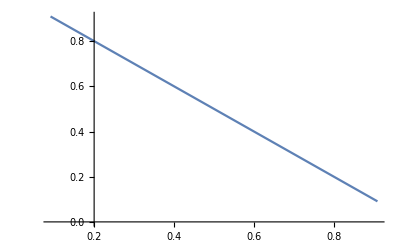

```mathematica
Plot[f[x],{x,0.090909,0.909091}]
```